```mathematica
result=Integrate[Sin[h]^2,{h,0,hp}]
resulteq=Integrate[Sin[h]^2,{h,hp,Pi/2}]
total=Integrate[Sin[h]^2,{h,0,Pi/2}]
```

1/2 (hp-Cos[hp] Sin[hp])

1/4 (-2 hp+π+Sin[2 hp])

π/4

```mathematica
FindRoot[resulteq/total==1/4,{hp,Pi/4}]
```

{hp→1.37184}

```mathematica
Solve[Pi/2-Pi/x==1.37184,x]
```

{{x→15.7904}}

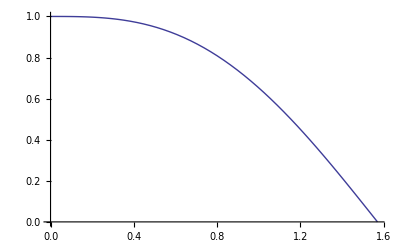

```mathematica
Plot[resulteq/total,{hp,0,Pi/2}]
```

```mathematica
192/2
```

96

A/(1+B Abs[Cos[h]]^1.)

A

A/(1+B)

{{B→-(-mumax+mumin)/mumin,A→mumax}}

{mumax→50,mumin→4}

50/(1+23/2 Abs[Cos[h]]^1.)

{{B→23/2,A→50}}

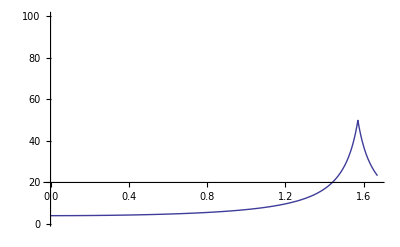

```mathematica
Clear[A,B,h]
fun=A/(1+B*Abs[Cos[h]]^(1.0))
fun1=fun//.{h->Pi/2}
fun2=fun//.{h->0}
sol=Solve[{fun1==mumax,fun2==mumin},{A,B}]
consts={mumax->50,mumin->4}
funplot=fun//.sol[[1]]//.consts
sol//.consts
Plot[funplot,{h,0,Pi/2+.1},PlotRange->{1,100}]
```

```mathematica
funplot//.{h->Pi/2+.001}
```

36.666

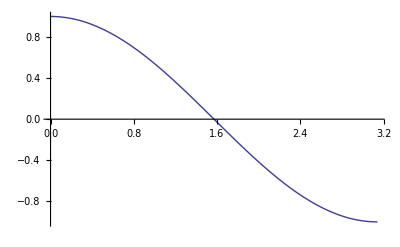

```mathematica
Plot[Cos[h],{h,0,Pi}]
```

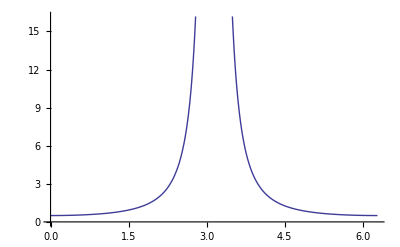

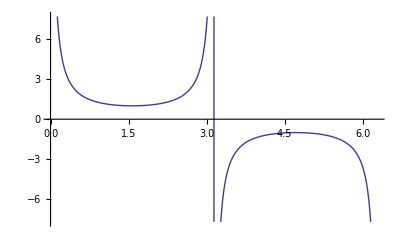

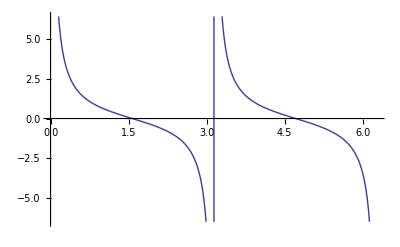

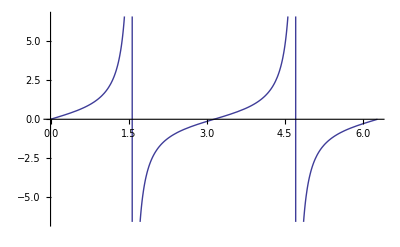

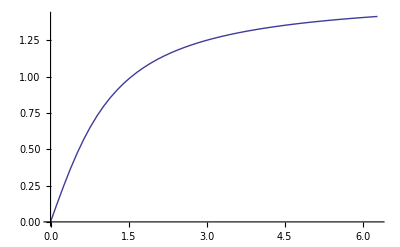

A-0.539641 B

-Graphics-

```mathematica
Plot[1/Sin[h],{h,0,2*Pi}]
Plot[1/Tan[h],{h,0,2*Pi}]
Plot[Tan[h],{h,0,2*Pi}]
Plot[ArcTan[h],{h,0,2*Pi}]
```

```mathematica
mu = \gamma_0 + A*Sin[h]^2/rho
```

```mathematica
Clear[A,B,CC,h]
shift=Pi/4+Pi/8
fun=(A-B*Exp[-(h-shift)^2])/(0.5+Sin[h]^2)
fun=(A-B*Exp[-(h-shift)^2])
fun1=fun//.{h->0}
fun2=fun//.{h->shift}
sol=FullSimplify[Solve[{fun1==mu1,fun2==mu0},{A,B}]]
finalfun=N[fun//.sol[[1]]//.{mu1->1/4,mu0->1/50/2}]
modit=If[h<shift,1.0,1+10*(h-shift)]
newfinalrho=finalfun*modit
finalmu=Sin[h]^2/finalfun
newfinalmu=Sin[h]^2/newfinalrho
```

(3 π)/8

(A-B ⅇ^(-(h-(3 π)/8)^2))/(0.5+Sin[h]^2)

A-B ⅇ^(-(h-(3 π)/8)^2)

A-B ⅇ^(-(9 π^2)/64)

A-B

{{A→mu1+(-mu0+mu1)/(-1+ⅇ^((9 π^2)/64)),B→(ⅇ^((9 π^2)/64) (-mu0+mu1))/(-1+ⅇ^((9 π^2)/64))}}

0.329828-0.0798276 2.71828^(1.38791-1. (-1.1781+h)^2)

If[h<(3 π)/8,1.,1+10 (h-shift)]

(0.329828-0.0798276 2.71828^(1.38791-1. (-1.1781+h)^2)) If[h<(3 π)/8,1.,1+10 (h-shift)]

Sin[h]^2/(0.329828-0.0798276 2.71828^(1.38791-1. (-1.1781+h)^2))

Sin[h]^2/((0.329828-0.0798276 2.71828^(1.38791-1. (-1.1781+h)^2)) If[h<(3 π)/8,1.,1+10 (h-shift)])

```mathematica
CForm[finalfun]
```

0.32982756514931555 - 0.07982756514931552*
    Power(2.718281828459045,1.387913118903191 - 1.*Power(-1.1780972450961724 + h,2))

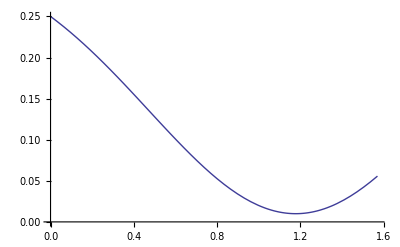

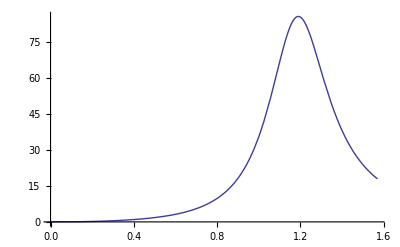

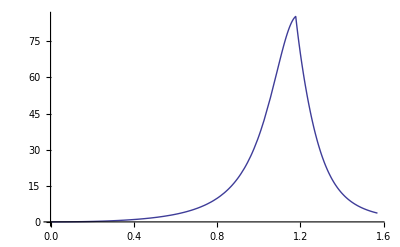

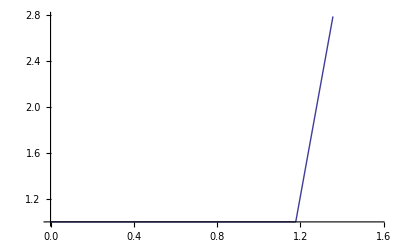

```mathematica
Plot[finalfun,{h,0,Pi/2}]
Plot[finalmu,{h,0,Pi/2}]
Plot[newfinalmu,{h,0,Pi/2}]
Plot[modit,{h,0,Pi/2}]
```

```mathematica
newfinalmu//.{h->Pi/2}
```

3.64344

```mathematica
rns=10*km
0.1*pc/rns
```

1000000

3.086×10^11

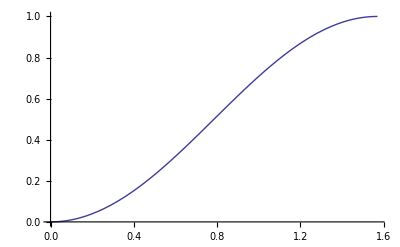

```mathematica
Plot[Sin[h]^2,{h,0,Pi/2}]
```

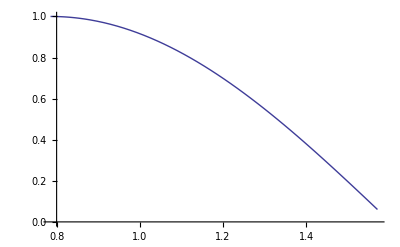

```mathematica
Plot[Cos[(h-Pi/4)/0.52],{h,Pi/4,Pi/2},PlotRange->{0,1}]
```

```mathematica
(* Crab *)
```

```mathematica
rns=10*km
tau=33/1000.
f=1/tau
omega=2*Pi*f
omegacodecrab=omega/(c/rns)
omegacodecurrent=3/4
omegacodecgs=omegacodecurrent*(c/rns)
```

1000000

0.033

30.303

190.4

0.00635105

3/4

22484.4

```mathematica
omegacodecurrent/omegacodecrab
```

118.091

```mathematica
2000+10*(120+60)
```

3800

```mathematica
ergPmev
```

1.60218×10^-6